## Icosahedron

```mathematica
phi=(1+Sqrt[5])/2
```

1/2 (1+√5)

```mathematica
normalize[x_]:=x/Norm[x]
```

```mathematica
Pts1={{0,1,phi},{0,1,-phi},{0,-1,phi},{0,-1,-phi}};Pts2=Map[RotateLeft,Pts1];
Pts3=Map[RotateLeft,Pts2];
IPts=Join[Pts1,Pts2,Pts3];
IPts=Map[normalize,IPts]//Simplify;
PtPerm={7,5,1,9,3,6,8,4,12,2,11,10};
```

```mathematica
IPts=IPts[[PtPerm]];
```

```mathematica
SpherePts[PTS_,r_:.03]:=Map[Sphere[#,r]&,PTS]
```

```mathematica
PlotSpherePts[pts_,opt_:{}]:=Graphics3D[{RGBColor[0,1,1],Sphere[{0,0,0}], RGBColor[1,0,0],SpherePts[pts],opt}]
```

```mathematica
PlotSpherePts[IPts]
```

-Graphics3D-

### Nearest Neighbor Info

```mathematica
GMat[X_]:=Table[ (X[[i]]-X[[j]]).(X[[i]]-X[[j]]),{i,1,Length[X]},{j,1,Length[X]}]//FullSimplify
```

```mathematica
G=GMat[IPts];
NNtbl=Table[
iDist=G[[i]];
nnDist=Drop[iDist,{i}]//Min;
ind=Flatten[Position[iDist,nnDist]],{i,1,12}]
```

{{2,3,9,10,12},{1,3,4,10,11},{1,2,4,5,12},{2,3,5,6,11},{3,4,6,7,12},{4,5,7,8,11},{5,6,8,9,12},{6,7,9,10,11},{1,7,8,10,12},{1,2,8,9,11},{2,4,6,8,10},{1,3,5,7,9}}

```mathematica
nbrhd[i_]:={IPts[[i]],IPts[[NNtbl[[i]]]]}
```

```mathematica
myArg[a_,b_,r_]:= Mod[Arg[N[a.b/(Norm[a]Norm[b])+I*Cross[a,b].r/(Norm[a]Norm[b])]],2Pi]
```

```mathematica
ArgList[neighbors_]:=
Map[myArg[neighbors[[2,1]],#,neighbors[[1]]]&,Drop[Map[#-neighbors[[2,1]]&,neighbors[[2]]],1]]
```

```mathematica
nbrhd[3]
```

{{0,√(2/(5+√5)),(1+√5)/(√(2 (5+√5)))},{{-√(2/(5+√5)),(1+√5)/(√(2 (5+√5))),0},{√(2/(5+√5)),(1+√5)/(√(2 (5+√5))),0},{(1+√5)/(√(2 (5+√5))),0,√(2/(5+√5))},{0,-√(2/(5+√5)),(1+√5)/(√(2 (5+√5)))},{-(1+√5)/(√(2 (5+√5))),0,√(2/(5+√5))}}}

```mathematica
ordind[i_]:=Module[{nbrarg},
nbrarg=ArgList[nbrhd[i]];Flatten[Map[Position[nbrarg,#]&,Sort[nbrarg]]]]
```

```mathematica
ordNN[[5]]
```

Part::partd: Part specification ordNN⟦5⟧ is longer than depth of object.

ordNN⟦5⟧

```mathematica
ordNN=Table[
Join[{NNtbl[[j,1]]},Drop[NNtbl[[j]],1][[ordind[j]]]],{j,1,12}];
```

```mathematica
midpts[Pts_]:=Map[normalize,(Pts+RotateRight[Pts])]
```

```mathematica
PlotSpherePts[IPts,Flatten[{RGBColor[0,1,0],SpherePts[IPts[[ordNN[[3]]]]],RGBColor[0,0,1],SpherePts[midpts[IPts[[ordNN[[3]]]]]]}]]
```

-Graphics3D-

```mathematica
ordNN[[1]]
```

{2,10,9,12,3}

```mathematica
Tri[j_]:=Table[Join[{j},Take[RotateLeft[ordNN[[j]],k],2]],{k,0,4}]
```

```mathematica
tris=Union[Flatten[Table[Tri[i],{i,1,12}],1],SameTest->(Length[Union[#1,#2]]==3 &)]
```

{{1,2,10},{1,3,2},{1,9,12},{1,10,9},{1,12,3},{2,3,4},{2,4,11},{2,11,10},{3,5,4},{3,12,5},{4,5,6},{4,6,11},{5,7,6},{5,12,7},{6,7,8},{6,8,11},{7,9,8},{7,12,9},{8,9,10},{8,10,11}}

```mathematica
Length[tris]
```

20

```mathematica
oppvert[v_,edge_]:=Complement[Flatten[Select[tris,Length[Intersection[#,edge]]==2&]],Append[edge,v]][[1]]
```

## Barycenter Coords to Sphere

### Stuff

```mathematica
trilabels={{1,2,3},{4,3,2},{3,4,5},{6,5,4},{5,6,7},{8,7,6},{7,8,9},{10,9,8},{9,10,1},{2,1,10},{2,11,4},{4,11,6},{6,11,8},{8,11,10},{10,11,2},{3,12,1},{5,12,3},{7,12,5},{9,12,7},{1,12,9}};
```

```mathematica
uplabels={{1,2,3},{3,4,5},{5,6,7},{7,8,9},{9,10,1},{2,11,4},{4,11,6},{6,11,8},{8,11,10},{10,11,2}};
downlabels={{4,3,2},{6,5,4},{8,7,6},{10,9,8},{2,1,10},{3,12,1},{5,12,3},{7,12,5},{9,12,7},{1,12,9}};
```

```mathematica
BC2SphereTri[alphaList_][trilab_]:=Map[normalize[#.IPts[[trilab]]]&,alphaList]
```

```mathematica
BC2Sphere[upalpha_,downalpha_]:=Module[{upPts,downPts},
upPts=Flatten[Map[BC2SphereTri[upalpha],uplabels],1];
downPts=Flatten[Map[BC2SphereTri[downalpha],downlabels],1];
{upPts,downPts}]
```

{upts,dpts}=BC2Sphere[{{.5,.5,0},{1/3,1/3,1/3}},{{.2,.2,.6}}];

```mathematica
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts,.02],RGBColor[1,1,0],SpherePts[dpts,.02]}]
```

-Graphics3D-

### Plane Triangle Routines

```mathematica
e[0]={1,0};
e[1]={1/2,Sqrt[3]/2};
```

```mathematica
Clear[x,y,ptri]
perp[{x_,y_}]={-y,x}
```

{-y,x}

```mathematica
func[{v0_,v1_,v2_}][x_]:=Module[{w},w=perp[v1-v0];
w.(x-v1)/(w.(v2-v1))]
```

```mathematica
PtinOpenTri[tri_][x_]:=(func[tri][x]>0&&func[RotateLeft[tri]][x]>0&&func[RotateLeft[tri,2]][x]>0)
```

```mathematica
PtinClosedTri[tri_][x_]:=(func[tri][x]>=0&&func[RotateLeft[tri]][x]>=0&&func[RotateLeft[tri,2]][x]>=0)
```

```mathematica
PlaneTri[j_]:=ptris[[j]]

SphereTri[j_]:=IPts[[trilabels[[j]]]]
```

```mathematica
TriLine[{a_,b_,c_}]:=Line[{a,b,c,a}]
```

```mathematica
Tri2a[ptri_][x_]:=Module[{a1,a2,a3},
{a2,a3}=Inverse[Transpose[{ptri[[2]]-ptri[[1]],ptri[[3]]-ptri[[1]]}]].(x-ptri[[1]]);
a1=1-a2-a3;
{a1,a2,a3}]
```

```mathematica
lattice[m_,n_]:=Module[{lattpts,ConvHullVerts,u0,u1,xmin,xmax,ymin,ymax},
u0=m*e[0]+n*e[1];
u1=(m+n)e[0]-m*e[1];
ConvHullVerts={{0,0},2u0,2u0+4u1,u0+5u1,-u0+5u1,-u0+u1};
xmin=Min[ConvHullVerts[[All,1]]]-1;
xmax=Max[ConvHullVerts[[ All,1]]]+1;
ymin=Min[ConvHullVerts[[All,2]]]-1;
ymax=Max[ConvHullVerts[[ All,2]]]+1;
lattpts=Flatten[Table[i*e[0]+j*e[1],{j,-(5m+n+1),2n+1},{i,-1,6m+5n+1}],1];
Select[lattpts,((xmin<#[[1]]<xmax) && (ymin<#[[2]]<ymax))&]
]
```

```mathematica
IcoPlaneVerts[m_,n_]:=Module[{u,v,z1,z2},
u[0]=m*e[0]+n*e[1];
u[1]=RotationMatrix[-Pi/3].u[0];
u[2]=u[1]-u[0];
v={{0,0},u[0],u[1],u[0]+u[1],2u[1],u[0]+2u[1],3u[1],u[0]+3u[1],4u[1],u[0]+4u[1],5u[1],u[0]+5u[1]};
z1={2u[0],2u[0]+u[1],2u[0]+2u[1],2u[0]+3u[1],2u[0]+4u[1]};
z2={u[2],u[2]+u[1],u[2]+2u[1],u[2]+3u[1],u[2]+4u[1]};
Join[v,z1,z2]]

IcoPlaneTris[m_,n_]:=Module[{v,z1,z2},
v=IcoPlaneVerts[m,n];
z1=Take[v, {13,17}];
z2=Take[v, {18,22}];
 Join[Table[v[[{k,k+1,k+2}]],{k,1,10}],
Table[{v[[2k]],z1[[k]],v[[2k+2]]},{k,1,5}],Table[{v[[2k-1]],v[[2k+1]],z2[[k]]},{k,1,5}]]]
```

```mathematica
Clear[latt,ptris]
GetBC[m_,n_]:=Module[{ latt, ptris},
latt=lattice[m,n];
     ptris=IcoPlaneTris[m,n];
Map[Tri2a[ptris[[1]]],Select[latt,PtinOpenTri[ptris[[1]]]]]]

GetFullBC[m_,n_]:=Module[{ latt, ptris, bc},
latt=lattice[m,n];
     ptris=IcoPlaneTris[m,n];
bc=Map[Tri2a[ptris[[1]]],Select[latt,PtinClosedTri[ptris[[1]]]]];
Select[bc,(Not[MemberQ[#,1]]&&(#[[2]]≠0))&]]
```

```mathematica
GetFullBC[m_,n_]:=Module[{ latt, ptris, bc},
latt=lattice[m,n];
     ptris=IcoPlaneTris[m,n];
bc=Map[Tri2a[ptris[[1]]],Select[latt,PtinClosedTri[ptris[[1]]]]];
Select[bc,(Not[MemberQ[#,1]])&]]
```

```mathematica
UpDownBC[m_,n_]:=Module[{bc},
bc=GetFullBC[m,n];
{Select[bc,#[[1]]≠0&],Select[bc,(#[[2]]≠0 &&#[[3]]≠0)&]}]
```

## Optimization

### Random stuff

```mathematica
RVec[n_]:=Partition[Table[Random[],{3n}],3]
```

```mathematica
RandBC[n_]:=Map[#/Total[#]&, RVec[n]]
```

### Energy functional:

```mathematica
Clear[Y]
En[s_][Y_]:=Sum[Norm[(Y[[k]]-Y[[j]])]^(-s),{k,1,Length[Y]-1},{j,k+1,Length[Y]}]
```

```mathematica
RPts=RVec[2000];
```

```mathematica
Timing[En[.5][RPts]]
```

{9.60302,2.63771×10^6}

Note that En is the sum over i>j and so the sum over i!=j  is 2En.

```mathematica
En2[s_][Y_]:=Module[{j,ev,Y1,Y2,one},
Y1=Table[Drop[Y,j],{j,1,Length[Y]-1}];
Y2=Table[Table[Y[[j]],{Length[Y]-j}],{j,1,Length[Y]-1}];
Total[(Map[Norm,Flatten[Y1-Y2,1]])^-s]
]
```

```mathematica
Timing[En2[.5][RPts]]
```

{3.71239,2.63771×10^6}

### Numerical Optimization: FindMinimum

#### Setup for general number of points. There are m+1 points with one point being fixed at {0,0}.

```mathematica
vec[x_,m_]:=Table[ToExpression[StringJoin[ToString[x],ToString[i]]],{i,1,m}]
vec[t,20]
```

{t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14,t15,t16,t17,t18,t19,t20}

```mathematica
Clear[xyvars,m,avars]
avars[m_]:=Flatten[Transpose[{vec[Theta,m],vec[Phi,m]}]]
avars[20]
```

{Theta1,Phi1,Theta2,Phi2,Theta3,Phi3,Theta4,Phi4,Theta5,Phi5,Theta6,Phi6,Theta7,Phi7,Theta8,Phi8,Theta9,Phi9,Theta10,Phi10,Theta11,Phi11,Theta12,Phi12,Theta13,Phi13,Theta14,Phi14,Theta15,Phi15,Theta16,Phi16,Theta17,Phi17,Theta18,Phi18,Theta19,Phi19,Theta20,Phi20}

```mathematica
addcoord[ab_]:=Transpose[Append[Transpose[Partition[ab,2]],Map[1-Total[#]&,Partition[ab,2]]]]
addcoord[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}]
```

{{1,2,-2},{3,4,-6},{5,6,-10},{7,8,-14},{9,10,-18},{11,12,-22},{13,14,-26},{15,16,-30},{17,18,-34},{19,20,-38}}

```mathematica
dropcoord[abc_]:=Flatten[Transpose[Drop[Transpose[abc],-1]]]
dropcoord[{{1,2,-2},{3,4,-6},{5,6,-10},{7,8,-14},{9,10,-18},{11,12,-22},{13,14,-26},{15,16,-30},{17,18,-34},{19,20,-38}}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Clear[f,ab,abc,Y]
f[s_][ab_]:=Module[{abc,Y},
abc=N[addcoord[ab]];
Y=Join[N[IPts],Apply[Join,BC2Sphere[abc,abc]]];
En[s][Y]]
```

```mathematica
Clear[f,ab,abc,Y]
fAll[s_][ab_]:=Module[{abc,Y},
abc=N[addcoord[ab]];
Y=Join[N[IPts],Apply[Join,BC2Sphere[abc,abc]]]]
```

```mathematica
Clear[minEnPts,minEnPtsAll]
minEnPtsAll[s_,abstart_]:=Module[{sol,m,c},
m=Length[abstart]/2;
sol=Apply[FindMinimum[f[s][avars[m]],##,MaxIterations->200]&,Transpose[{avars[m],abstart}] ];
c=addcoord[(avars[m]/.sol[[2]])];
Join[N[IPts],Apply[Join,BC2Sphere[c,c]]]]
```

```mathematica
minEnPts[s_,abstart_]:=Module[{sol,m,c},
m=Length[abstart]/2;
sol=Apply[FindMinimum[f[s][avars[m]],##,MaxIterations->200]&,Transpose[{avars[m],abstart}] ];
addcoord[(avars[m]/.sol[[2]])]]
```

```mathematica
a2Pt[a_]:=a[[1]]e[0]+a[[2]]e[1]
```

## Examples

```mathematica
config34=fAll[2.0][dropcoord[aa]];
```

```mathematica
config=SetPrecision[minEnPtsAll[2.0,dropcoord[aa]],6];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
SetDirectory[NotebookDirectory[]];
Export["config34m.txt",config,"Table"]
```

config34m.txt

#### (m, n) = (3, 4)

```mathematica
vlab={1,2,3,4,5,6,7,8,9,10,1,2};
```

```mathematica
mm=3;nn=4;
latt=lattice[mm,nn];
ptris=IcoPlaneTris[mm,nn];
vv=IcoPlaneVerts[mm,nn];
zz1=Take[vv, {13,17}];
zz2=Take[vv, {18,22}];
```

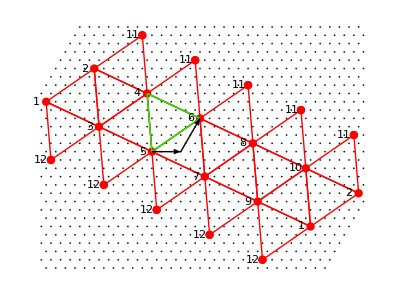

```mathematica
Show[Graphics[{PointSize[.003],Map[Point,latt],RGBColor[1,0,0],PointSize[.015],Map[Point,Join[vv,zz1,zz2]],Map[TriLine,ptris],RGBColor[0,1,0],TriLine[PlaneTri[4]],RGBColor[0,0,0],
{Thin,Arrow[{vv[[5]],vv[[5]]+mm*e[0]}],Arrow[{vv[[5]]+mm*e[0],vv[[5]]+mm*e[0]+nn*e[1]}]},Table[Text[vlab[[k]],vv[[k]]-{1,0}],{k,1,Length[vlab]}],Table[Text[11,zz1[[k]]-{1,0}],{k,1,Length[zz1]}],Table[Text[12,zz2[[k]]-{1,0}],{k,1,Length[zz2]}]}]]
```

```mathematica
Table[Text[vlab[[k]],vv[[k]]-{1,0}],{k,1,Length[vlab]}]
```

{Text[1,{-1,0}],Text[2,{4,2 √3}],Text[3,{9/2,-(3 √3)/2}],Text[4,{19/2,(√3)/2}],Text[5,{10,-3 √3}],Text[6,{15,-√3}],Text[7,{31/2,-(9 √3)/2}],Text[8,{41/2,-(5 √3)/2}],Text[9,{21,-6 √3}],Text[10,{26,-4 √3}],Text[1,{53/2,-(15 √3)/2}],Text[2,{63/2,-(11 √3)/2}]}

```mathematica
aa=N[GetFullBC[mm,nn]]
```

{{0.27027,0.027027,0.702703},{0.0810811,0.108108,0.810811},{0.540541,0.0540541,0.405405},{0.351351,0.135135,0.513514},{0.162162,0.216216,0.621622},{0.810811,0.0810811,0.108108},{0.621622,0.162162,0.216216},{0.432432,0.243243,0.324324},{0.243243,0.324324,0.432432},{0.0540541,0.405405,0.540541},{0.702703,0.27027,0.027027},{0.513514,0.351351,0.135135},{0.324324,0.432432,0.243243},{0.135135,0.513514,0.351351},{0.405405,0.540541,0.0540541},{0.216216,0.621622,0.162162},{0.027027,0.702703,0.27027},{0.108108,0.810811,0.0810811}}

```mathematica
Length[aa]
```

18

```mathematica
{upts,dpts}= BC2Sphere[aa,aa];
```

```mathematica
Length[dpts]
```

180

```mathematica
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts,.015],RGBColor[1,1,0],SpherePts[dpts,.015]}]
```

-Graphics3D-

```mathematica
Timing[naa=minEnPts[2.0,dropcoord[aa]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{245.579,{{0.285316,0.0308541,0.68383},{0.0970123,0.127308,0.77568},{0.530215,0.0589778,0.410807},{0.353761,0.14486,0.501378},{0.176075,0.233949,0.589976},{0.77568,0.0970117,0.127308},{0.589976,0.176075,0.233949},{0.420368,0.249096,0.330536},{0.249096,0.330536,0.420367},{0.0589778,0.410808,0.530215},{0.68383,0.285316,0.030854},{0.501379,0.353761,0.14486},{0.330537,0.420367,0.249096},{0.144861,0.501378,0.353761},{0.410808,0.530215,0.0589775},{0.23395,0.589975,0.176075},{0.0308542,0.68383,0.285316},{0.127308,0.775679,0.0970126}}}

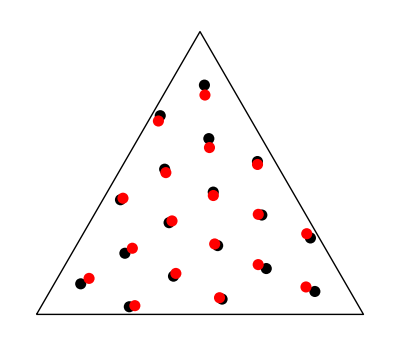

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa]}]]
```

```mathematica
{nupts,ndpts}=BC2Sphere[naa,naa];
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[nupts,.015],RGBColor[1,1,0],SpherePts[ndpts,.015]}]
```

-Graphics3D-

```mathematica
laa=Length[GetBC[mm,nn]]
Timing[tbl=Table[naaR=minEnPts[2.0,dropcoord[aaR=RandBC[laa]]];{f[2][dropcoord[naaR]],naaR,aaR},{5}];]
```

18

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 200 iterations.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 200 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

{1122.98,Null}

```mathematica
tbl[[All,1]]
```

{97139.2,97813.4,97248.4,97745.4,96554.8}

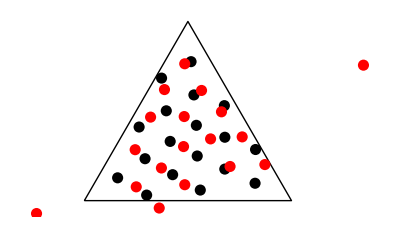

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,naa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,tbl[[4,2]]]}]]
```

### GetFullBC Example

```mathematica
a1=GetFullBC[2,2]
```

{{1/2,0,1/2},{1/6,1/6,2/3},{2/3,1/6,1/6},{1/3,1/3,1/3},{0,1/2,1/2},{1/2,1/2,0},{1/6,2/3,1/6}}

```mathematica
d=Join[c[[1]],c[[2]]]
```

{{1/6,1/6,2/3},{2/3,1/6,1/6},{1/3,1/3,1/3},{1/2,1/2,0},{1/6,2/3,1/6},{1/6,1/6,2/3},{2/3,1/6,1/6},{1/3,1/3,1/3},{0,1/2,1/2},{1/6,2/3,1/6}}

```mathematica
c=UpDownBC[2,2]
```

{{{1/6,1/6,2/3},{2/3,1/6,1/6},{1/3,1/3,1/3},{1/2,1/2,0},{1/6,2/3,1/6}},{{1/6,1/6,2/3},{2/3,1/6,1/6},{1/3,1/3,1/3},{0,1/2,1/2},{1/6,2/3,1/6}}}

```mathematica
BC2Sphere[c[[1]],c[[2]]];
```

```mathematica
{upts,dpts}= FullSimplify[BC2Sphere[{{1/2,0,1/2},{1/6,1/6,2/3},{2/3,1/6,1/6},{1/3,1/3,1/3},{1/2,1/2,0},{1/6,2/3,1/6}},{{1/6,1/6,2/3},{2/3,1/6,1/6},{1/3,1/3,1/3},{0,1/2,1/2},{1/6,2/3,1/6}}]];
```

```mathematica
{upts,dpts}= Apply[BC2Sphere,UpDownBC[8,8]];
```

```mathematica
Intersection[upts,dpts]
```

{}

```mathematica
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts,.015],RGBColor[1,1,0],SpherePts[dpts,.015]}]
```

-Graphics3D-

### First Attempt to map to sphere

```mathematica
Clear[a1,a2,a3,p1,ptri,stri,j]
Tri2Sphere[ptri_,stri_][x_]:=Module[{a},
a=Tri2a[ptri][x];
normalize[ a[[1]]stri[[1]]+a[[2]]stri[[2]]+a[[3]]stri[[3]]]]
```

```mathematica
pptri=PlaneTri[6];
sstri=SphereTri[6];
Map[Tri2Sphere[pptri,sstri],Select[latt,PtinTri[pptri]]][[All,1,1]]//N
```

{}

```mathematica
Tri2Sphere[PlaneTri[1],SphereTri[1]][PlaneTri[1][[1]]]-SphereTri[1][[1]]//N
```

{0.,0.,0.}

```mathematica
Clear[ptri,stri,thelattice]
SphereLatticeTriPts[ptri_,stri_,thelattice_]:=Simplify[Map[Tri2Sphere[ptri,stri],Select[thelattice,PtinTri[ptri]]]]
```

```mathematica
Clear[k]
SLatPts=Apply[Join,Table[SphereLatticeTriPts[PlaneTri[k],SphereTri[k],latt],{k,1,20}]];

PlotSpherePts[IPts,{RGBColor[0,0,1],SpherePts[{IPts[[12]]}],RGBColor[1,1,0],SpherePts[IPts[[{1,3}]]],RGBColor[0,0,0],SpherePts[SLatPts,.02]}]
```

-Graphics3D-

### Density

```mathematica
g[a1_,a2_]:=
Module[{x,p1,p2,p3,w},
p1=IPts[[1]];
p2=IPts[[2]];
p3=IPts[[3]];
w=normalize[(p1+p2+p3)];
x=a1*p1+a2*p2+(1-a1-a2)*p3;
w.x/x.x]



f[x_]:=Module[{a1,a2},
{a1,a2}=Inverse[Transpose[{u[0],u[1]}]].x;
g[a1,a2]]
```

```mathematica
f[{x1,x2}]//FullSimplify
```

Transpose::nmtx: The first two levels of {u[0],u[1]} cannot be transposed.

Set::shape: Lists {a1$35006,a2$35006} and Inverse[Transpose[{u[0],u[1]}]].{x1,x2} are not the same shape.

(√(10/3 (65+29 √5)))/(5 (3+√5)-4 (5+√5) a2$35006+4 (5+√5) (a1$35006^2+a1$35006 (-1+a2$35006)+a2$35006^2))

```mathematica
Factor[1905 (3+√5)+12 (5+√5) (-13+x1) x1-4 (5+√5) (√3-3 x2) x2]
```

5715+1905 √5-780 x1-156 √5 x1+60 x1^2+12 √5 x1^2-20 √3 x2-4 √15 x2+60 x2^2+12 √5 x2^2

```mathematica
p1=IPts[[1]];
p2=IPts[[2]];
p3=IPts[[3]];
w=normalize[(p1+p2+p3)];
```

```mathematica
(p1+p2+p3).(p1+p2+p3)/9.//Sqrt
```

0.794654

```mathematica
a1=.33;a2=.33;x=a1*p1+a2*p2+(1-a1-a2)*p3;
w.x/(Norm[x])
```

0.999971

```mathematica
g[1.,0]
g[0,1.]
```

0.794654

0.794654

```mathematica
g[0,0.]
```

0.794654

```mathematica
Clear[a1,a2,a3]
Plot3D[g[a1,a2],{a2,0,1},{a1,0,1-a2}]
```

-Graphics3D-

```mathematica
Plot3D[N[f[{x,y}]],{y,0,Sqrt[3]/2},{x,y/Sqrt[3],1-y/Sqrt[3]}]
```

Set::shape: Lists {a1$37758,a2$37758} and Inverse[Transpose[{u[0],u[1]}]].{0.,0.0000619208} are not the same shape.

Set::shape: Lists {a1$38023,a2$38023} and Inverse[Transpose[{u[0],u[1]}]].{0.,0.0619209} are not the same shape.

Set::shape: Lists {a1$38288,a2$38288} and Inverse[Transpose[{u[0],u[1]}]].{0.,0.12378} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

-Graphics3D-

```mathematica
f[{1/4,0}]
```

Set::shape: Lists {a1$39265,a2$39265} and Inverse[Transpose[{u[0],u[1]}]].{1/4,0} are not the same shape.

(((1+√5)^2 (1-a1$39265-a2$39265))/(2 (5+√5) √((1+√5)^2/(2 (5+√5))+(√(2/(5+√5))+(1+√5) √(2/(5+√5)))^2))+((√(2/(5+√5))+(1+√5) √(2/(5+√5))) (((1+√5) a1$39265)/(√(2 (5+√5)))+√(2/(5+√5)) (1-a1$39265-a2$39265)+((1+√5) a2$39265)/(√(2 (5+√5)))))/(√((1+√5)^2/(2 (5+√5))+(√(2/(5+√5))+(1+√5) √(2/(5+√5)))^2)))/(((1+√5)^2 (1-a1$39265-a2$39265)^2)/(2 (5+√5))+(-√(2/(5+√5)) a1$39265+√(2/(5+√5)) a2$39265)^2+(((1+√5) a1$39265)/(√(2 (5+√5)))+√(2/(5+√5)) (1-a1$39265-a2$39265)+((1+√5) a2$39265)/(√(2 (5+√5))))^2)

### (m,n)=(7,8)

```mathematica
aa=GetBC[7,8];
Length[aa]
```

84

```mathematica
Timing[naa=minEnPts[2.0,dropcoord[aa]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1041.81,{{0.14613,0.00707239,0.846798},{0.0521437,0.0590789,0.888777},{0.276599,0.0134927,0.709909},{0.189745,0.0624663,0.747788},{0.0986439,0.111814,0.789543},{0.398209,0.0197379,0.582053},{0.314159,0.0660897,0.619751},{0.229469,0.113143,0.657388},{0.141221,0.160332,0.698447},{0.042442,0.201624,0.755934},{0.516203,0.0262372,0.457559},{0.432189,0.0708781,0.496933},{0.349588,0.11535,0.535061},{0.266681,0.160522,0.572798},{0.180931,0.2059,0.613169},{0.087528,0.247736,0.664736},{0.634048,0.0337548,0.332197},{0.547896,0.0778851,0.374219},{0.465096,0.120303,0.414602},{0.383822,0.162579,0.453599},{0.302416,0.205724,0.491861},{0.218744,0.249417,0.531839},{0.129411,0.291222,0.579367},{0.0337546,0.332197,0.634049},{0.755934,0.0424423,0.201624},{0.664736,0.0875283,0.247736},{0.579367,0.129411,0.291222},{0.497669,0.169418,0.332913},{0.41774,0.209034,0.373226},{0.337736,0.249687,0.412577},{0.255766,0.29152,0.452713},{0.169418,0.332913,0.497669},{0.077885,0.374219,0.547896},{0.888777,0.0521438,0.0590789},{0.789542,0.0986441,0.111814},{0.698446,0.141222,0.160332},{0.613168,0.180931,0.205901},{0.531839,0.218744,0.249417},{0.452713,0.255767,0.291521},{0.373932,0.293347,0.332721},{0.293347,0.332721,0.373932},{0.209034,0.373226,0.41774},{0.120303,0.414601,0.465096},{0.0262371,0.457559,0.516203},{0.846798,0.14613,0.00707265},{0.747788,0.189746,0.0624666},{0.657388,0.229469,0.113143},{0.572797,0.266681,0.160522},{0.49186,0.302416,0.205724},{0.412577,0.337736,0.249687},{0.332721,0.373932,0.293348},{0.249686,0.412577,0.337736},{0.162579,0.453599,0.383823},{0.0708781,0.496933,0.432189},{0.709908,0.276599,0.013493},{0.619751,0.314159,0.06609},{0.535061,0.349589,0.11535},{0.453599,0.383823,0.162579},{0.373226,0.41774,0.209034},{0.29152,0.452713,0.255767},{0.205724,0.49186,0.302416},{0.11535,0.535061,0.349589},{0.019738,0.582053,0.398209},{0.582053,0.398209,0.0197381},{0.496933,0.432189,0.0708782},{0.414601,0.465096,0.120303},{0.332913,0.497669,0.169418},{0.249417,0.531839,0.218744},{0.160522,0.572797,0.266681},{0.0660899,0.619751,0.314159},{0.457559,0.516203,0.0262372},{0.374219,0.547896,0.0778851},{0.291222,0.579367,0.129411},{0.205901,0.613168,0.180931},{0.113143,0.657388,0.229469},{0.0134929,0.709909,0.276599},{0.332197,0.634049,0.0337547},{0.247736,0.664736,0.0875281},{0.160332,0.698446,0.141222},{0.0624666,0.747788,0.189745},{0.201624,0.755934,0.042442},{0.111814,0.789542,0.0986439},{0.00707266,0.846798,0.14613},{0.059079,0.888777,0.0521437}}}

```mathematica
naa78={{0.1461298058701171,0.007072392949488698,0.8467978011803943},{0.05214365285285369,0.059078878403715396,0.8887774687434309},{0.27659856103416025,0.013492692325116117,0.7099087466407237},{0.18974543032799024,0.06246630482213612,0.7477882648498737},{0.09864389316340237,0.11181355574161307,0.7895425510949845},{0.3982089269118333,0.019737940532996653,0.5820531325551701},{0.3141591262877283,0.06608974552582463,0.6197511281864471},{0.22946875412180992,0.11314312625748486,0.6573881196207052},{0.14122149886448357,0.16033175887660334,0.6984467422589131},{0.042441970715839376,0.2016238125844908,0.7559342166996699},{0.5162033664275678,0.02623716729906641,0.45755946627336574},{0.43218909659667293,0.07087812410449386,0.49693277929883317},{0.34958836032240503,0.11535019682115323,0.5350614428564417},{0.2666805013031884,0.16052181012935343,0.5727976885674582},{0.18093094793484332,0.20590036103268813,0.6131686910324685},{0.08752799801272712,0.24773551641148314,0.6647364855757898},{0.634048494364224,0.03375480744039498,0.3321966981953811},{0.5478959362734093,0.0778851184353472,0.37421894529124355},{0.46509563830110157,0.12030274293393942,0.41460161876495905},{0.38382236380820395,0.16257873236746673,0.4535989038243293},{0.30241569097418797,0.2057236560620739,0.49186065296373815},{0.21874420080342094,0.24941669489459603,0.531839104301983},{0.12941072634918074,0.29122211291787137,0.5793671607329479},{0.033754630270059933,0.33219671772083453,0.6340486520091055},{0.7559339317227424,0.042442310296067876,0.2016237579811897},{0.6647361189680602,0.08752825437542926,0.2477356266565106},{0.5793667686541245,0.12941091865048698,0.29122231269538856},{0.4976688004221053,0.16941789980341185,0.3329132997744828},{0.41773952772437356,0.20903408167740628,0.37322639059822016},{0.33773607160485397,0.24968650165188505,0.4125774267432609},{0.25576643339027455,0.2915203722532391,0.4527131943564864},{0.16941774535280035,0.33291305509543373,0.4976691995517659},{0.0778850026232649,0.3742188227499681,0.547896174626767},{0.8887773231592725,0.052143774576134165,0.059078902264593336},{0.7895422232797206,0.0986441231452001,0.11181365357507933},{0.6984462940106175,0.1412217641842638,0.16033194180511867},{0.6131681974666859,0.18093117231455563,0.20590063021875848},{0.5318386045551202,0.21874440448408328,0.2494169909607965},{0.45271271035690047,0.2557666097372786,0.291520679905821},{0.3739315190683082,0.2933474991259911,0.33272098180570064},{0.2933473681094841,0.33272065393215583,0.3739319779583601},{0.20903397475472482,0.37322609364779746,0.4177399315974777},{0.12030265243799977,0.4146014320803107,0.4650959154816895},{0.026237119759050957,0.4575594334736797,0.5162034467672694},{0.8467975271863943,0.146129825685463,0.007072647128142595},{0.7477878296009576,0.18974559232641489,0.062466578072627565},{0.6573876067998793,0.22946896745181233,0.11314342574830838},{0.5727971670670625,0.2666807090469009,0.1605221238860366},{0.4918601563889813,0.30241588921764345,0.20572395439337532},{0.41257695721576837,0.33773625608333563,0.24968678670089606},{0.33272056630281654,0.3739316709818603,0.29334776271532315},{0.24968646242063147,0.4125770768712868,0.3377364607080817},{0.16257871362450796,0.4535986266445674,0.38382265973092466},{0.07087813016713107,0.4969326464066301,0.4321892234262388},{0.7099084278752631,0.2765985906325017,0.013492981492235212},{0.6197507658231441,0.3141592421604414,0.06608999201641441},{0.5350610657676469,0.34958851329988966,0.1153504209324634},{0.4535985332617135,0.383822526454676,0.16257894028361042},{0.3732260510508123,0.417739686198821,0.20903426275036674},{0.2915203894836748,0.45271285624740987,0.25576675426891526},{0.20572372407530717,0.49186029649760304,0.30241597942708975},{0.11535028972087565,0.5350611968619502,0.3495885134171741},{0.0197380286105197,0.5820530348727149,0.3982089365167655},{0.5820529691089117,0.39820894772222704,0.019738083168861276},{0.4969325881637057,0.43218919683457935,0.07087821500171487},{0.41460141469662587,0.4650957497379912,0.1203028355653829},{0.33291308883358106,0.49766893754715785,0.16941797361926114},{0.24941681193937257,0.5318387564853782,0.21874443157524925},{0.1605219865755525,0.572797347735983,0.2666806656884645},{0.06608992216971432,0.6197508984181713,0.31415917941211435},{0.4575594112723447,0.5162034025823173,0.026237186145337987},{0.3742188594594284,0.5478960155368914,0.07788512500368028},{0.2912222145524647,0.5793669191408137,0.1294108663067215},{0.20590055558637993,0.6131683598881943,0.18093108452542572},{0.11314337848364375,0.657387780106894,0.22946884140946222},{0.013492943281301763,0.709908525504622,0.2765985312140762},{0.33219678274571546,0.6340485462283115,0.03375467102597307},{0.24773567378022604,0.6647362673320755,0.08752805888769855},{0.16033197871764393,0.698446442702257,0.1412215785800991},{0.06246659044033796,0.7477879591250469,0.1897454504346151},{0.20162389602291247,0.7559340744575462,0.04244202951954135},{0.11181374886141539,0.7895423261527134,0.09864392498587127},{0.0070726623118064266,0.8467975944248335,0.14612974326336003},{0.05907899135714429,0.8887773550632496,0.05214365357960604}};
```

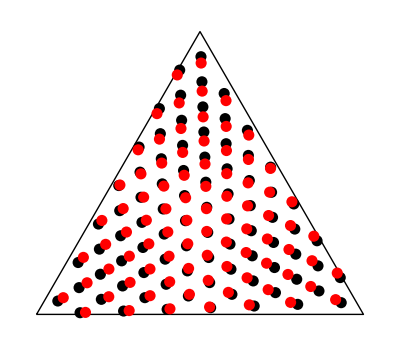

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa78]}]]
```

```mathematica
{upts78,dpts78}= BC2Sphere[naa78,naa78];
```

```mathematica
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts78,.015],RGBColor[1,1,0],SpherePts[dpts78,.015]}]
```

-Graphics3D-

### (m,n) = (5,4)

```mathematica
aa=GetBC[5,4];
Length[aa]
```

30

```mathematica
Timing[naa54=minEnPts[2.0,dropcoord[aa]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{73.8685,{{0.0987511,0.0801326,0.821116},{0.324414,0.0553831,0.620202},{0.183089,0.147654,0.669257},{0.0189671,0.230499,0.750534},{0.534354,0.0362846,0.429361},{0.396735,0.122682,0.480582},{0.259704,0.208244,0.532052},{0.108672,0.29053,0.600798},{0.750534,0.0189673,0.230499},{0.600797,0.108673,0.29053},{0.464518,0.189865,0.345617},{0.331714,0.267324,0.400962},{0.189865,0.345617,0.464518},{0.0362845,0.429361,0.534354},{0.821116,0.0987511,0.0801327},{0.669256,0.183089,0.147654},{0.532051,0.259704,0.208244},{0.400962,0.331714,0.267324},{0.267324,0.400962,0.331714},{0.122682,0.480582,0.396735},{0.620202,0.324414,0.0553832},{0.480582,0.396735,0.122682},{0.345617,0.464518,0.189866},{0.208244,0.532051,0.259704},{0.0553832,0.620202,0.324414},{0.429361,0.534354,0.0362846},{0.29053,0.600797,0.108673},{0.147654,0.669256,0.183089},{0.230499,0.750534,0.0189672},{0.0801327,0.821116,0.0987511}}}

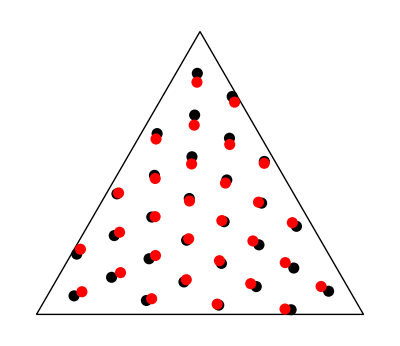

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa54]}]]
```

```mathematica
{upts54,dpts54}=BC2Sphere[naa54,naa54];
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts54,.015],RGBColor[1,1,0],SpherePts[dpts54,.015]}]
```

-Graphics3D-

### (m,n)=(4,3)

```mathematica
aa=GetBC[4,3];
Length[aa]
```

18

```mathematica
Timing[naa43=minEnPts[2.0,dropcoord[aa]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{21.4684,{{0.127308,0.0970126,0.77568},{0.410807,0.058978,0.530215},{0.233949,0.176075,0.589976},{0.0308534,0.285316,0.68383},{0.68383,0.0308535,0.285316},{0.501378,0.14486,0.353761},{0.330536,0.249097,0.420367},{0.14486,0.353761,0.501379},{0.77568,0.127308,0.0970127},{0.589976,0.233949,0.176075},{0.420367,0.330536,0.249097},{0.249097,0.420367,0.330536},{0.058978,0.530215,0.410807},{0.530215,0.410807,0.0589781},{0.353761,0.501378,0.14486},{0.176075,0.589976,0.233949},{0.285316,0.68383,0.0308534},{0.0970127,0.77568,0.127308}}}

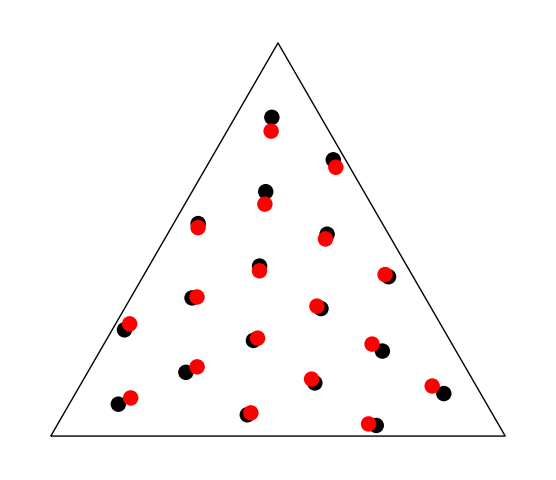

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa43]}]]
```

```mathematica
{upts43,dpts43}=BC2Sphere[naa43,naa43];
```

```mathematica
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts43,.015],RGBColor[1,1,0],SpherePts[dpts43,.015]}]
```

-Graphics3D-

### (m,n)=(2,3)

```mathematica
aa=GetBC[2,3];
```

```mathematica
Timing[naa23=minEnPts[2.0,dropcoord[aa]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{4.02473,{{0.373968,0.058965,0.567067},{0.121076,0.17961,0.699313},{0.699313,0.121077,0.17961},{0.455952,0.217187,0.326861},{0.217187,0.326861,0.455952},{0.567067,0.373968,0.058965},{0.326861,0.455952,0.217188},{0.058965,0.567067,0.373968},{0.17961,0.699313,0.121076}}}

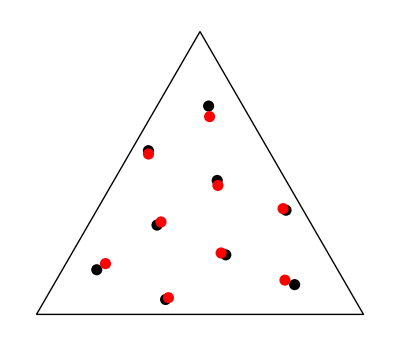

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa23]}]]
```

```mathematica
{upts23,dpts23}=BC2Sphere[naa23,naa23];
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts23,.015],RGBColor[1,1,0],SpherePts[dpts23,.015]}]
```

-Graphics3D-

### (m,n)=(3,3)

```mathematica
aa=GetBC[3,3]
```

{{1/9,1/9,7/9},{4/9,1/9,4/9},{2/9,2/9,5/9},{7/9,1/9,1/9},{5/9,2/9,2/9},{1/3,1/3,1/3},{1/9,4/9,4/9},{4/9,4/9,1/9},{2/9,5/9,2/9},{1/9,7/9,1/9}}

```mathematica
Timing[naa33=minEnPts[2.0,dropcoord[aa]]]
```

$Aborted

```mathematica
1086.495749/60
```

18.1083

```mathematica
RandBC[n_]:=Map[#/Total[#]&, RVec[n]]
```

```mathematica
Length[aa]
```

10

```mathematica
Timing[tbl33=Table[naa33R=minEnPts[2.0,dropcoord[aaR=RandBC[10]]];{f[2][dropcoord[naa33R]],naa33R,aaR},{2}];]
```

{108.75,Null}

```mathematica
tbl33[[All,1]]
```

{28206.2,28762.5}

```mathematica
f[2.][dropcoord[naa33]]
f[2.][dropcoord[naa33R]]
```

28247.9

28206.2

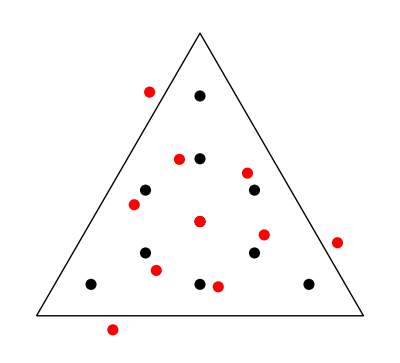

```mathematica
naa33R=tbl33[[1,2]];Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa33R]}]]
```

```mathematica
{upts33R,dpts33R}=BC2Sphere[naa33R,naa33R];
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts33R,.015],RGBColor[1,1,0],SpherePts[dpts33R,.015]}]
```

-Graphics3D-

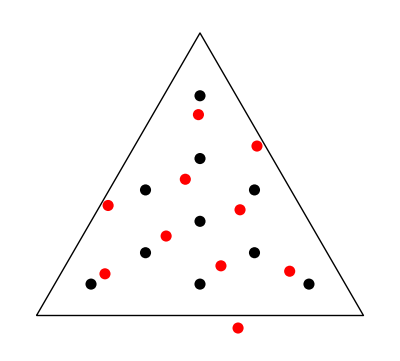

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa33]}]]
```

```mathematica
{upts33,dpts33}=BC2Sphere[naa33,naa33];
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts33,.015],RGBColor[1,1,0],SpherePts[dpts33,.015]}]
```

-Graphics3D-

### (m,n)=(3,3)

```mathematica
aa=GetFullBC[3,3]
```

{{1/9,1/9,7/9},{4/9,1/9,4/9},{2/9,2/9,5/9},{0,1/3,2/3},{7/9,1/9,1/9},{5/9,2/9,2/9},{1/3,1/3,1/3},{1/9,4/9,4/9},{2/3,1/3,0},{4/9,4/9,1/9},{2/9,5/9,2/9},{0,2/3,1/3},{1/3,2/3,0},{1/9,7/9,1/9}}

```mathematica
Length[aa]
```

14

```mathematica
Timing[naa33=minEnPts[2.0,dropcoord[aa]]]
```

FindMinimum::fmdig: Working precision MachinePrecision is insufficient to achieve the requested accuracy or precision.

{22.8026,{{0.111111,0.111111,0.777778},{0.444444,0.111111,0.444444},{0.222222,0.222222,0.555556},{0.0000150799,0.333348,0.666637},{0.777778,0.111111,0.111111},{0.555556,0.222222,0.222222},{0.333333,0.333333,0.333333},{0.111111,0.444444,0.444444},{0.666677,0.333343,-0.0000199862},{0.444444,0.444444,0.111111},{0.222222,0.555556,0.222222},{0.0000270151,0.666694,0.333279},{0.333355,0.666689,-0.0000438566},{0.111111,0.777778,0.111111}}}

```mathematica
RandBC[n_]:=Map[#/Total[#]&, RVec[n]]
```

```mathematica
Length[aa]
```

10

```mathematica
dropcoord[aa]
```

{1/9,1/9,4/9,1/9,2/9,2/9,0,1/3,7/9,1/9,5/9,2/9,1/3,1/3,1/9,4/9,2/3,1/3,4/9,4/9,2/9,5/9,0,2/3,1/3,2/3,1/9,7/9}

```mathematica
Timing[tbl33=Table[naa33R=minEnPts[2.0,dropcoord[aaR=RandBC[10]]];{f[2][dropcoord[naa33R]],naa33R},{3}];]
```

{111.704,Null}

```mathematica
tbl33[[All,1]]
```

{28206.2,28449.2,28206.2}

```mathematica
f[2.][dropcoord[naa33]]
f[2.][dropcoord[naa33R]]
```

28247.9

28206.2

```mathematica
naa33R=tbl33[[1,2]];Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa33R]}]]
```

-Graphics-

```mathematica
{upts33,dpts33}=BC2Sphere[naa33,naa33];
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts33,.015],RGBColor[1,1,0],SpherePts[dpts33,.015]}]
```

-Graphics3D-

```mathematica
Intersection[upts33,dpts33]
```

{}

```mathematica
Show[Graphics[{PointSize[.02],Line[{{0,0},e[0],e[1],{0,0}}],Map[Point[a2Pt[#]]&,aa], RGBColor[1,0,0],Map[Point[a2Pt[#]]&,naa33]}]]
```

-Graphics-

```mathematica
{upts33,dpts33}=BC2Sphere[naa33,naa33];
PlotSpherePts[IPts,{RGBColor[0,0,0],SpherePts[upts33,.015],RGBColor[1,1,0],SpherePts[dpts33,.015]}]
```

-Graphics3D-

### Misc. Input

```mathematica
x
```

```mathematica
{0.,0.7401781116328517,0.2892212748396935}
```

```mathematica
multi[{v1_,v2_,v3_},k_]:=Module[{i1,i2,i3},
Union[Flatten[Table[v1^i1*v2^i2*v3^i3,{i1,0,k},{i2,0,k-i1}, {i3,0,k-i1-i2}]]]]
```

```mathematica
v[[1]]
```

Part::partd: Part specification v ⟦ 1 ⟧ is longer than depth of object.

v⟦1⟧

```mathematica
multi[vec[u,3],3]
```

{1,u1,u1^2,u1^3,u2,u1 u2,u1^2 u2,u2^2,u1 u2^2,u2^3,u3,u1 u3,u1^2 u3,u2 u3,u1 u2 u3,u2^2 u3,u3^2,u1 u3^2,u2 u3^2,u3^3}

```mathematica
naa[[All,3]]
```

{0.846798,0.888777,0.709909,0.747788,0.789543,0.582053,0.619751,0.657388,0.698447,0.755934,0.457559,0.496933,0.535061,0.572798,0.613169,0.664736,0.332197,0.374219,0.414602,0.453599,0.491861,0.531839,0.579367,0.634049,0.201624,0.247736,0.291222,0.332913,0.373226,0.412577,0.452713,0.497669,0.547896,0.0590789,0.111814,0.160332,0.205901,0.249417,0.291521,0.332721,0.373932,0.41774,0.465096,0.516203,0.00707265,0.0624666,0.113143,0.160522,0.205724,0.249687,0.293348,0.337736,0.383823,0.432189,0.013493,0.06609,0.11535,0.162579,0.209034,0.255767,0.302416,0.349589,0.398209,0.0197381,0.0708782,0.120303,0.169418,0.218744,0.266681,0.314159,0.0262372,0.0778851,0.129411,0.180931,0.229469,0.276599,0.0337547,0.0875281,0.141222,0.189745,0.042442,0.0986439,0.14613,0.0521437}

```mathematica
data[i_]:=N[Transpose[Append[Transpose[aa],naa[[All,i]]]]]
```

```mathematica
Clear[x]
Table[ Fit[data[i],multi[vec[u,3],4],vec[u,3]] ,{i,1,3}]
```

{0.0218881+0.100615 u1+0.187647 u1^2+0.28591 u1^3+0.395673 u1^4+0.0156478 u2+0.202575 u1 u2+0.524175 u1^2 u2+1.03238 u1^3 u2+0.00447614 u2^2+0.323772 u1 u2^2+1.11529 u1^2 u2^2-0.0103822 u2^3+0.413153 u1 u2^3-0.0289067 u2^4+0.0158468 u3+0.195245 u1 u3+0.511786 u1^2 u3+0.972256 u1^3 u3+0.00351085 u2 u3+0.534973 u1 u2 u3+1.1112 u1^2 u2 u3-0.037577 u2^2 u3+1.59712 u1 u2^2 u3-0.0678844 u2^3 u3+0.00623804 u3^2+0.319341 u1 u3^2+1.26997 u1^2 u3^2-0.0352678 u2 u3^2+1.30385 u1 u2 u3^2-0.377517 u2^2 u3^2-0.00909184 u3^3+0.373981 u1 u3^3-0.0412865 u2 u3^3-0.0293373 u3^4,0.0218881+0.0158468 u1+0.00623807 u1^2-0.00909183 u1^3-0.0293374 u1^4+0.100615 u2+0.195245 u1 u2+0.319341 u1^2 u2+0.373982 u1^3 u2+0.187647 u2^2+0.511786 u1 u2^2+1.26996 u1^2 u2^2+0.28591 u2^3+0.972258 u1 u2^3+0.395672 u2^4+0.0156478 u3+0.00351086 u1 u3-0.035267 u1^2 u3-0.0412845 u1^3 u3+0.202575 u2 u3+0.534973 u1 u2 u3+1.30386 u1^2 u2 u3+0.524175 u2^2 u3+1.1112 u1 u2^2 u3+1.03238 u2^3 u3+0.00447609 u3^2-0.0375778 u1 u3^2-0.377516 u1^2 u3^2+0.323772 u2 u3^2+1.59712 u1 u2 u3^2+1.11529 u2^2 u3^2-0.0103822 u3^3-0.0678866 u1 u3^3+0.413152 u2 u3^3-0.0289066 u3^4,0.0218881+0.0156478 u1+0.0044761 u1^2-0.0103822 u1^3-0.0289066 u1^4+0.0158468 u2+0.00351097 u1 u2-0.037577 u1^2 u2-0.0678848 u1^3 u2+0.00623802 u2^2-0.0352678 u1 u2^2-0.377516 u1^2 u2^2-0.00909185 u2^3-0.0412871 u1 u2^3-0.0293373 u2^4+0.100615 u3+0.202576 u1 u3+0.323772 u1^2 u3+0.413152 u1^3 u3+0.195245 u2 u3+0.534975 u1 u2 u3+1.59713 u1^2 u2 u3+0.319341 u2^2 u3+1.30386 u1 u2^2 u3+0.373981 u2^3 u3+0.187647 u3^2+0.524176 u1 u3^2+1.11529 u1^2 u3^2+0.511786 u2 u3^2+1.11121 u1 u2 u3^2+1.26996 u2^2 u3^2+0.28591 u3^3+1.03238 u1 u3^3+0.972258 u2 u3^3+0.395672 u3^4}

```mathematica
Clear[v,k]
```

```mathematica
k=2;
Table[v1^i1*v2^i2*v3^i3, {i1,0,2},{i2,0,2-i1} ,{i3,0,2-i1-i2}]
```

{{{1,v3,v3^2},{v2,v2 v3},{v2^2}},{{v1,v1 v3},{v1 v2}},{{v1^2}}}

```mathematica
{{{1,v3,v3^2},{v2,v2 v3},{v2^2}},{{v1,v1 v3},{v1 v2}},{{v1^2}}}
```

{{{1,v3,v3^2},{v2,v2 v3},{v2^2}},{{v1,v1 v3},{v1 v2}},{{v1^2}}}

```mathematica
multi[v,2]
```

multi[v,2]